```mathematica
Id[d_]:=IdentityMatrix[d];γe=1.76086 10^8;

σ={{1/2.({{0, 1}, {1, 0}}),1/2.({{0, -ⅈ}, {ⅈ, 0}}),1/2.({{1, 0}, {0, -1}})},{1/(√2.)({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),1/(√2.)({{0, -ⅈ, 0}, {ⅈ, 0, -ⅈ}, {0, ⅈ, 0}}),({{1., 0, 0}, {0, 0, 0}, {0, 0, -1.}})}};

M1_⊗M2_:=KroneckerProduct[M1,M2]; M1_⊗M2_⊗M3_:=(M1⊗M2)⊗M3;

HyperfineHamiltonian[n_,spin_,hfc_]:=(
If[n==0,M=1; 
S=Table[σ[[1,p]],{p,3}]; Table[0,{2},{2}],
M=Product[spin[[k]],{k,1,n}]; II=Table[(Id[Product[spin[[k]],{k,1,j-1}]])⊗σ[[spin[[j]]-1,p]]⊗(Id[Product[spin[[k]],{k,j+1,n}]]),{j,n},{p,3}];
S=Table[σ[[1,p]]⊗Id[M],{p,3}];
Sum[hfc[[j,p,q]] σ[[1,p]]⊗II[[j,q]],{j,n},{p,3},{q,3}]  ]
);

ZeemanHamiltonian[ω0_,θ0_,ϕ0_]:=(
ω0(S[[1]] Sin[θ0]Cos[ϕ0]+S[[2]] Sin[θ0]Sin[ϕ0]+S[[3]] Cos[θ0])
);

TY[nA_,spinA_,hfcA_,nB_,spinB_,hfcB_,ω0_,θ0_,ϕ0_,ks_,kt_,krA_,krB_]:=(
HA=HyperfineHamiltonian[nA,spinA,hfcA]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MA=M;SA=S//Chop;
HB=HyperfineHamiltonian[nB,spinB,hfcB]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MB=M;SB=S//Chop;
M=MA MB;
H=HA⊗Id[2 MB]+Id[2 MA]⊗HB;
PS=0.25 Id[4 M]-SA[[1]]⊗SB[[1]]-SA[[2]]⊗SB[[2]]-SA[[3]]⊗SB[[3]];
PT=0.75 Id[4 M]+SA[[1]]⊗SB[[1]]+SA[[2]]⊗SB[[2]]+SA[[3]]⊗SB[[3]];
IS = (1/(3*M))PT;
ISV=Transpose[{Flatten[IS]}];
KK=(ks/2)*(PS⊗Id[4M]+Id[4M]⊗Transpose[PS])+(kt/2)*(PT⊗Id[4M]+Id[4M]⊗Transpose[PT]);
RR=krA*((3/4)*(Id[4M]⊗Id[4M])-SA[[1]]⊗Id[2MB]⊗Transpose[SA[[1]]⊗Id[2MB]]-SA[[2]]⊗Id[2MB]⊗Transpose[SA[[2]]⊗Id[2MB]]-SA[[3]]⊗Id[2MB]⊗Transpose[SA[[3]]⊗Id[2MB]])+krB*((3/4)*(Id[4M]⊗Id[4M])-Id[2MA]⊗SB[[1]]⊗Transpose[Id[2MA]⊗SB[[1]]]-Id[2MA]⊗SB[[2]]⊗Transpose[Id[2MA]⊗SB[[2]]]-Id[2MA]⊗SB[[3]]⊗Transpose[Id[2MA]⊗SB[[3]]]);
HH=H⊗Id[4 M]-Id[4 M]⊗Transpose[H];
LL=ⅈ*HH+KK+RR;
rhov =Inverse[LL].ISV;
rho = ArrayReshape[rhov,{4M,4M}];
kt*Re[Tr[PT.rho]]//Chop  
);
```

## Isotropic hyperfine coupling constants (HFCC) data for FADH^.

### Lee at el. (Alternative radical pairs for cryptochrome-based magnetoreception)

Nucleus | HFCC (mT)
H5 | -0.8029
N5 | 0.4313
H8(X3) | 0.2554
N10 | 0.2506
Hβ | 0.1908

## Figure 2(b) - 0.15-0.55 mT (Single HFI-H5)

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^4;
PAa=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.15,0.55},PlotRange->All,PlotStyle->{Brown,Dotted},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 5.0*10^4;
PAb=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.15,0.55},PlotRange->All,PlotStyle->{Magenta,DotDashed},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 5.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^5;
PAc=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.15,0.55},PlotRange->All,PlotStyle->{Cyan},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^5s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

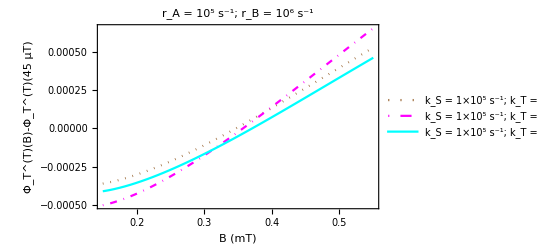

```mathematica
Show[PAa,PAb,PAc]
```

## Figure 3 - 0.0-1.0 mT (Single HFI-H5)

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^4;
PBa=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,1.0},PlotRange->All,PlotStyle->{Brown,Dotted},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 5.0*10^4;
PBb=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,1.0},PlotRange->All,PlotStyle->{Magenta,DotDashed},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 5.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^5;
PBc=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,1.0},PlotRange->All,PlotStyle->{Cyan},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^5s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

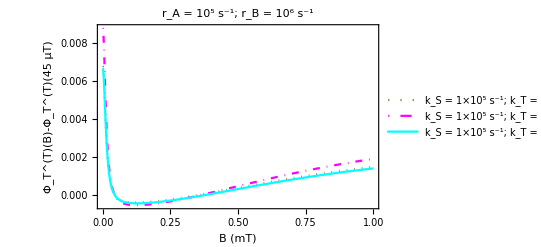

```mathematica
Show[PBa,PBb,PBc]
```

## Figure 5 - 0.15-0.55 mT (5 HFI-H5,N5,3xH8)

Fractional triplet yield was calculated using Advanced Research Computing (ARC) cluster at the University of Calgary. The obtained values are shown in the tables below.

### ks = 1.0*10^7; kt = 1.0*10^6;

```mathematica
nA=5;nB=0;
spinA={2,3,2,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.0 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.2 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.5 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.7 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.9 *γe,0,0,ks,kt,krA,krB];
```

```mathematica
{{B(mT), Subscript[Φ, T]^(T)(B)}, {0.0, 0.40692811}, {0.045, 0.324567391}, {0.2, 0.3105352}, {0.5, 0.326882527}, {0.7, 0.356003429}, {0.9, 0.378919939}}
```

```mathematica
change5a={{0,0.082360719},{0.2,-0.01403219},{0.5,0.002315136},{0.7,0.031436038},{0.9,0.054352548}};PCa=ListPlot[change5a,PlotRange->All,PlotMarkers->{"△",PointSize[0.06]},PlotStyle->{Black},PlotLegends->{"k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"5 HFIs
r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

### ks = 1.0*10^7; kt = 5.0*10^5;

```mathematica
nA=5;nB=0;
spinA={2,3,2,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.0 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.2 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.5 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.7 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.9 *γe,0,0,ks,kt,krA,krB];
```

```mathematica
{{B(mT), Subscript[Φ, T]^(T)(B)}, {0.0, 0.281780175}, {0.045, 0.202571888}, {0.2, 0.194541599}, {0.5, 0.207779569}, {0.7, 0.230570692}, {0.9, 0.249559271}}
```

```mathematica
change5b={{0,0.079208286},{0.2,-0.008030289},{0.5,0.005207681},{0.7,0.027998803},{0.9,0.046987383}};PCb=ListPlot[change5b,PlotRange->All,PlotMarkers->{"□",PointSize[0.06]},PlotStyle->{Blue},PlotLegends->{"k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"5 HFIs
r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

### ks = 5.0*10^6; kt = 2.0*10^6;

```mathematica
nA=5;nB=0;
spinA={2,3,2,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.0 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.2 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.5 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.7 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.9 *γe,0,0,ks,kt,krA,krB];
```

```mathematica
{{B(mT), Subscript[Φ, T]^(T)(B)}, {0.0, 0.650393252}, {0.045, 0.601898111}, {0.2, 0.594458218}, {0.5, 0.60496605}, {0.7, 0.623153826}, {0.9, 0.636510445}}
```

```mathematica
change5c={{0,0.048495141},{0.2,-0.007439893},{0.5,0.003067939},{0.7,0.021255715},{0.9,0.034612334}};PCc=ListPlot[change5c,PlotRange->All,PlotMarkers->{"◇",PointSize[0.06]},PlotStyle->{Red},PlotLegends->{"k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"5 HFIs
r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

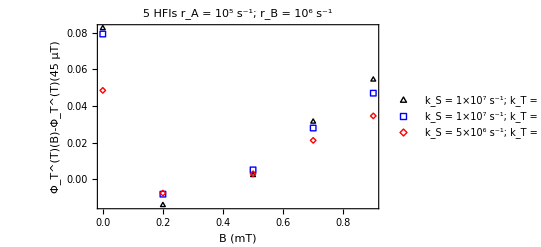

```mathematica
Show[PCa,PCb,PCc]
```

## Supporting Information

#### Figure-S1(a)

```mathematica
change5a={{0,0.082360719},{0.2,-0.01403219},{0.5,0.002315136},{0.7,0.031436038},{0.9,0.054352548}};P5a=ListPlot[change5a,PlotRange->All,PlotMarkers->{"★",PointSize[0.06]},PlotStyle->{Black},PlotLegends->{"5 HFI (H5, N5, 3 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
nA=4;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
P4a=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"◇",PointSize[0.06]},PlotStyle->{Magenta},PlotLegends->{"4 HFI (H5, N5, 2 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
P3a=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"△",PointSize[0.06]},PlotStyle->{Blue},PlotLegends->{"3 HFI (H5, N5, 1 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,3,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2506, 0, 0}, {0, 0.2506, 0}, {0, 0, 0.2506}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
P3aa=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"▽",PointSize[0.06]},PlotStyle->{Cyan},PlotLegends->{"3 HFI (H5, N5, N10)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
P2a=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"□",PointSize[0.06]},PlotStyle->{Green},PlotLegends->{"2 HFI (H5, N5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
P1a=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"○",PointSize[0.05]},PlotStyle->{Red},PlotLegends->{"1 HFI (H5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
Show[P1a,P2a,P3a,P3aa,P4a,P5a]
```

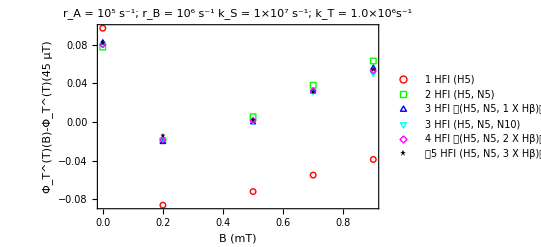

### Figure-S1(b)

```mathematica
change5b={{0,0.079208286},{0.2,-0.008030289},{0.5,0.005207681},{0.7,0.027998803},{0.9,0.046987383}};P5b=ListPlot[change5b,PlotRange->All,PlotMarkers->{"★",PointSize[0.06]},PlotStyle->{Black},PlotLegends->{"5 HFI (H5, N5, 3 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=4;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
P4b=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"◇",PointSize[0.06]},PlotStyle->{Magenta},PlotLegends->{"4 HFI (H5, N5, 2 X Hβ)"},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
P3b=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"△",PointSize[0.06]},PlotStyle->{Blue},PlotLegends->{"3 HFI (H5, N5, 1 X Hβ)"},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,3,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2506, 0, 0}, {0, 0.2506, 0}, {0, 0, 0.2506}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
P3bb=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"▽",PointSize[0.06]},PlotStyle->{Cyan},PlotLegends->{"3 HFI (H5, N5, N10)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
P2b=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"□",PointSize[0.06]},PlotStyle->{Green},PlotLegends->{"2 HFI (H5, N5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
P1b=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"○",PointSize[0.05]},PlotStyle->{Red},PlotLegends->{"1 HFI (H5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
Show[P1b,P2b,P3b,P3bb,P4b,P5b]
```

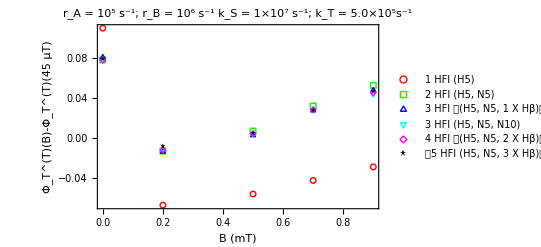

### Figure-S1(b)

```mathematica
change5c={{0,0.048495141},{0.2,-0.007439893},{0.5,0.003067939},{0.7,0.021255715},{0.9,0.034612334}};P5c=ListPlot[change5c,PlotRange->All,PlotMarkers->{"★",PointSize[0.06]},PlotStyle->{Black},PlotLegends->{"5 HFI (H5, N5, 3 X Hβ)"},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1"]
```

```mathematica
nA=4;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;
P4c=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"◇",PointSize[0.06]},PlotStyle->{Magenta},PlotLegends->{"4 HFI (H5, N5, 2 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;
P3c=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"△",PointSize[0.06]},PlotStyle->{Blue},PlotLegends->{"3 HFI (H5, N5, 1 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1"]
```

```mathematica
nA=3;nB=0;
spinA={2,3,3,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2506, 0, 0}, {0, 0.2506, 0}, {0, 0, 0.2506}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;
P3cc=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"▽",PointSize[0.06]},PlotStyle->{Cyan},PlotLegends->{"3 HFI (H5, N5, N10)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1"]
```

```mathematica
nA=2;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;
P2c=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"□",PointSize[0.06]},PlotStyle->{Green},PlotLegends->{"2 HFI (H5, N5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^□s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;;
P1c=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"○",PointSize[0.05]},PlotStyle->{Red},PlotLegends->{"1 HFI (H5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1"];
```

```mathematica
Show[P1c,P2c,P3c,P3cc,P4c,P5c]
```